## Parameters

```mathematica
ClearAll;
x0 =3;
NOrbit = 1;
Rabi = 0.33;
InitialS = Transpose[{Join[{1},Flatten[ConstantArray[0,{1,2NOrbit-1}]]]}];
ProjectionUp = Join[Join[ConstantArray[0,{NOrbit,NOrbit}], ConstantArray[0,{NOrbit,NOrbit}],2],Join[ConstantArray[0,{NOrbit,NOrbit}],DiagonalMatrix[Table[1,{i,0,NOrbit-1}]],2]];
H0 =DiagonalMatrix[Table[i,{i,0,NOrbit-1}]] ;
AnHarm =0* DiagonalMatrix[Table[-Exp[-(i-NOrbit)^2/10],{i,0,NOrbit-1}]];
Hc = Table[NIntegrate[HermiteH[i,x-x0]HermiteH[j,x+x0]Exp[-(x^2+x0^2)],{x,-20,20}]/(√(2^(i+j)i!j!)),{i,0,NOrbit-1},{j,0,NOrbit-1}]/NIntegrate[Exp[-x^2]HermiteH[0,x]HermiteH[0,x],{x,-20,20}];
```

```mathematica
Table[-Exp[-(i-NOrbit)^2/10],{i,0,NOrbit-1}]//N
```

{-0.0000453999,-0.000303539,-0.00166156,-0.00744658,-0.0273237,-0.082085,-0.201897,-0.40657,-0.67032,-0.904837}

## Rabi Oscillation

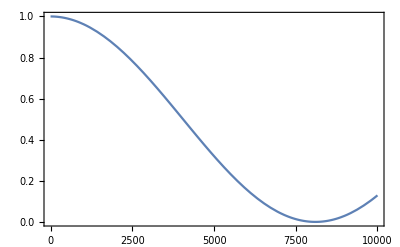

```mathematica
δ = 0.0;
H = Join[Join[H0, Rabi*Hc,2],Join[Rabi*Transpose[Hc],H0+δ*DiagonalMatrix[Table[1,{i,0,NOrbit-1}]]+AnHarm,2]];
PopulationT[t_]:=Module[{t0=t,P,FinalS},
FinalS =MatrixExp[ⅈ π H t0/2/Rabi].InitialS;
P=ConjugateTranspose[FinalS].ProjectionUp.ProjectionUp.FinalS;
1-Flatten[Abs[P]]
]
Plot[PopulationT[x],{x,0,10000},Frame->True,PlotRange->{{0,10000},{0,1}}]
```

## Lineshape

```mathematica
t = 1;(*in π*)
```

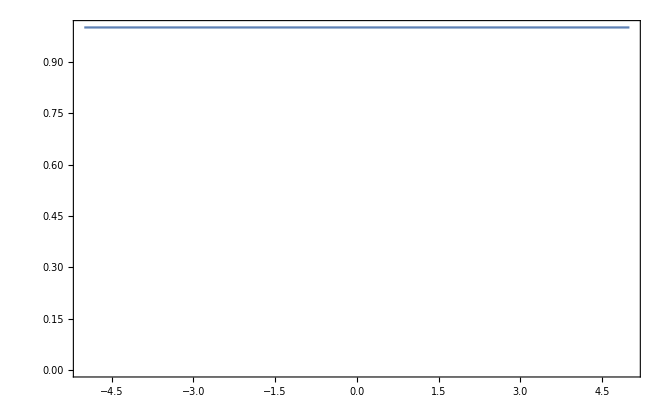

```mathematica
PopulationD[δ_]:=Module[{δ0=δ,P,H,FinalS},
H = Join[Join[H0,Rabi* Hc,2],Join[Rabi*Transpose[Hc],H0+δ0*DiagonalMatrix[Table[1,{i,0,NOrbit-1}]] +AnHarm,2]];
FinalS =MatrixExp[ⅈ π t H /2/Rabi].InitialS;
P=ConjugateTranspose[FinalS].ProjectionUp.ProjectionUp.FinalS;
1-Flatten[Abs[P]]
]
Plot[PopulationD[x],{x,-5,5},Frame->True,PlotRange->{{-5,5},{0,1}}]
```